```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Dada f[x_] y r se crea la trayectoria xt*)
f[x_]:=r x (1-x)


rs={1.5,2.9,3.3,3.5,3.55,3.59,3.83,4.};

Manipulate[
r = rs⟦k⟧;
lista = NestList[f,x0,nmax]; (*nmax: nro máximo de iteraciones*)
ListPlot[lista, Joined->join, Mesh->All, PlotRange->All, PlotLabel->"r = " <> ToString[rs⟦k⟧]]
,{x0,0,1},{k,1,Length[rs],1},{nmax,1,100,1},{join,{True, False}}]
```

```mathematica
(*Efecto de las condiciones iniciales*)

f[x_]:=r x (1-x)
rs={1.5,2.9,3.3,3.5,3.55,3.59,3.83,4.};
Manipulate[
r = rs⟦k⟧;
lista1 = NestList[f,x01,nmax]; (*nmax: nro máximo de iteraciones*)
g1 = ListPlot[lista1, Joined->join, Mesh->All, PlotRange->All, PlotLabel->"r = " <> ToString[rs⟦k⟧], PlotStyle->Red];
lista2 = NestList[f,x02,nmax]; (*nmax: nro máximo de iteraciones*)
g2 = ListPlot[lista2, Joined->join, Mesh->All, PlotRange->All, PlotLabel->"r = " <> ToString[rs⟦k⟧], PlotStyle->Blue];
lista3 = NestList[f,x03,nmax]; (*nmax: nro máximo de iteraciones*)
g3 = ListPlot[lista3, Joined->join, Mesh->All, PlotRange->All, PlotLabel->"r = " <> ToString[rs⟦k⟧], PlotStyle->Green];
lista4 = NestList[f,x04,nmax]; (*nmax: nro máximo de iteraciones*)
g4 = ListPlot[lista4, Joined->join, Mesh->All, PlotRange->All, PlotLabel->"r = " <> ToString[rs⟦k⟧], PlotStyle->Yellow];
Show[{g1,g2,g3, g4}, PlotRange->All]
,{x01,0,1},{x02,0,1},{x03,0,1},{x04,0,1},{k,1,Length[rs],1},{nmax,1,100,1},{join,{True,False}}]
```

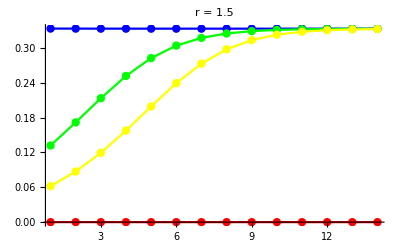

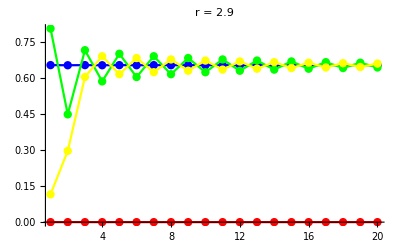

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification rs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

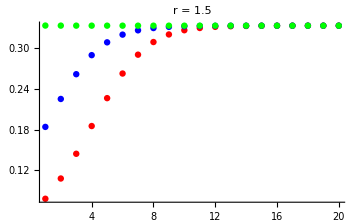
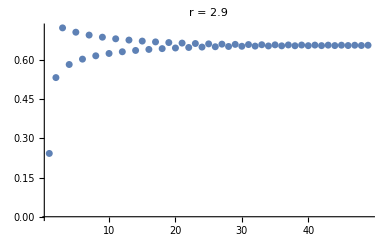
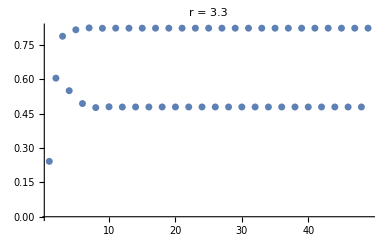
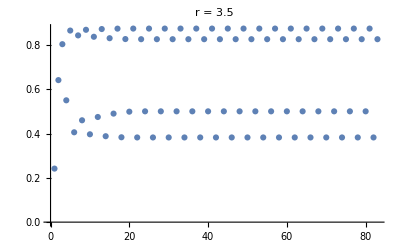
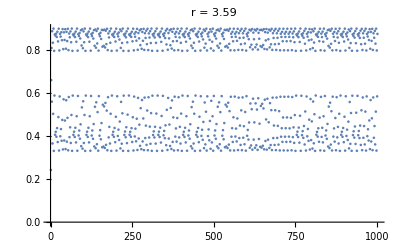
-Graphics--Graphics-
atractores: 0.3335								atractores: 0.6555

-Graphics-	-Graphics-
atractores:0.8235,0.4795							atractores:0.8745,0.5005,0.8265,0.3825
-Graphics-
atractores: infinitos

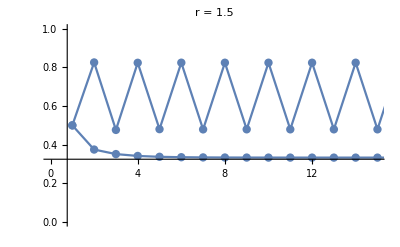

```mathematica
(*Grafico varias figuras juntas*)
f[x_]:=r x (1-x)

x0 =0.5;
nmax = 15;

rs={1.5,2.9,3.3,3.5,3.55,3.59,3.83,4.};
k = 1;
r = rs⟦k⟧;
lista = NestList[f,x0,nmax]; (*nmax: nro máximo de iteraciones*)
g1 = ListPlot[lista, Joined->True, Mesh->All, PlotRange->All, PlotLabel->"r = " <> ToString[rs⟦k⟧]];
k = 3;
r = rs⟦k⟧;
lista = NestList[f,x0,nmax]; (*nmax: nro máximo de iteraciones*)
g2 = ListPlot[lista, Joined->True, Mesh->All, PlotRange->All, PlotLabel->"r = " <> ToString[rs⟦k⟧]];
Show[g1,g2, PlotRange->{{0,nmax},{0,1}}]
```

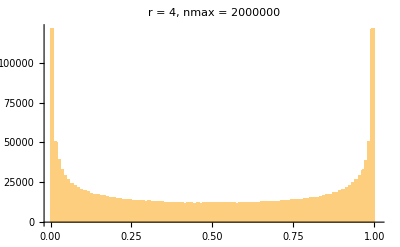

```mathematica
(*Histograma*)
(*Defino sobre qué r voy a trabajar, la cantidad total de iteraciones que haré y la cantidad de iteraciones que no se tienen en cuenta por formar parte del transitorio*)
r = 4;
nmax = 2000000;
ntransitorio = 100000;

(*Creo una lista de condiciones iniciales*)
cantx0 = 100;
x0s = RandomReal[{0,1},cantx0];
x0 = x0s⟦1⟧;

(*Itero*)
lista = NestList[f,x0,nmax]⟦ntransitorio+1;;⟧;
(*Histograma*)
bspec = 0.01; (*ancho de cada barra*)
Histogram[lista,{bspec}, PlotLabel->"r = " <> ToString[r] <> ", nmax = " <> ToString[nmax], PlotRange->{{0,1},{0,All}}]
```

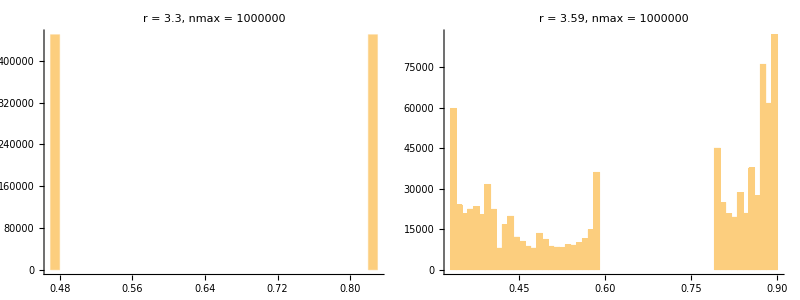

```mathematica
(*Búsqueda de atractores*)

Atractores[f_,r_,tol_,nmax_,ntransitorio_]:=Module[{x0, lista, positions, cantidad, cantidadmax, posmax, k, max, atractores,tolg},
(*Busca los atractores*)
x0 = RandomReal[{0,1},1];
(*Itero*)
lista = NestList[f,x0,nmax]⟦ntransitorio+1;;⟧;
(*Histograma*)
{{positions}, {cantidad}} = N[HistogramList[lista,{tol}]]; (*Busco la cantidad de datos de cada barra de ancho tol. La función me devuelve una lista formada a su vez por 2 listas: la primera indica la posición de inicio de cada barra y la segunda, la cantidad de datos en cada barra*)
(*Print[cantidad];*)

(*Busco los máximos de la lista cantidad*)
k=Length[cantidad];
cantidadmax = ConstantArray[0,k]; max = ConstantArray[0,k];
posmax = Ordering[cantidad,-k];   (*gives the positions in a list at which the first n elements of sort[list] appear.*)

Do[
cantidadmax⟦j⟧ = Extract[cantidad, posmax⟦j⟧];
max⟦j⟧ = (Extract[positions,posmax⟦j⟧+1] + Extract[positions,posmax⟦j⟧])/2; (*el máximo debe estar en la mitad*)
,{j,1,k}];

atractores = {};
tolg = 0.5; (*indica cuántos elementos tiene que tener una barra del histograma respecto a la siguiente para ser considerada como atractor*)
Do[
If[cantidadmax⟦-j-1⟧/cantidadmax⟦-j⟧ <tolg,
(*Print[cantidadmax⟦-j⟧, " - ", max⟦-j⟧]; *) AppendTo[atractores, max⟦-j⟧];Break[],
(*Print[cantidadmax⟦-j⟧," - ", max⟦-j⟧]]; *) AppendTo[atractores, max⟦-j⟧];],
{j,1,Length[cantidadmax]-1}];
(*Asumiendo que el atractor es el mismo para cualquier condición inicial, no hago promedio. Directamente tiro los primeros ntransitorio valores*)
atractores
]

(*Test de función*)
nmax = 100000;
ntransitorio = 0;
r = 2.22; (*rs⟦5⟧*)
f[x_]:=r x (1-x)
tol = 0.001;
Print["Atractores para r = ", ToString[r], ": ", Atractores[f,r,tol,nmax,ntransitorio]]
```

Atractores para r = 2.22: {0.5495}

```mathematica
(*Diagrama cobweb*)

rmin = 0.;
rmax =4. ;


Manipulate[
f[x_]:=r x (1-x);
f2[x_]:=f[f[x]];
f4[x_]:=f2[f2[x]];
f8[x_]:=f4[f4[x]];


lista = NestList[f,x0,nmax];


(*cobx y coby contienen los datos de x e y del diagrama cobweb*)
cobx = ConstantArray[0, 2 Length[lista]]; coby = ConstantArray[0, 2 Length[lista]];
Do[
cobx⟦2 k - 1⟧=lista⟦k⟧;
cobx⟦2 k⟧= lista⟦k⟧;
,{k,1,Length[lista]}];

coby⟦1⟧ =0;
Do[
coby⟦2 k⟧ = lista⟦k + 1⟧;
coby⟦2k + 1⟧ = lista⟦k + 1⟧;
,{k,1,Length[lista] - 1}
] ;
coby⟦-1⟧ = f[coby⟦-2⟧];

graphcob = ListPlot[Transpose[{cobx⟦ntransitorio+1;;⟧,coby⟦ntransitorio+1;;⟧}], Joined->True, Mesh->All, PlotStyle->Red];

graphf = Plot[f[x],{x,0,1}];
graphx = Plot[x,{x,0,1}];
graphfn = Plot[fn[x],{x,0,1}, PlotStyle->Black];
Show[graphf, graphx, graphfn,graphcob,PlotRange->{{0,1},{0,1}}, PlotLabel->"r = " <> ToString[r]]
,{r,rmin,rmax},{x0,0,1},{nmax,1,10,1},{ntransitorio,0,nmax,1}, {fn,{0,f2,f4,f8}}]
```

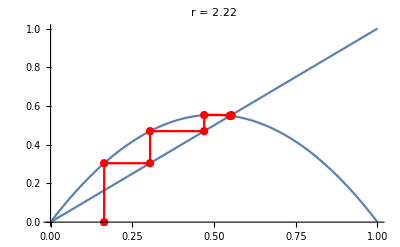
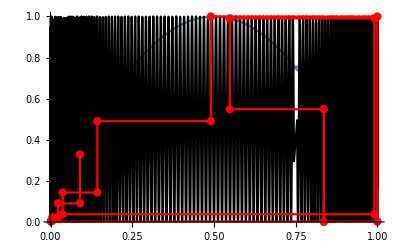
-Graphics-
Jugando encontré el siguiente gráfico. Bastante turbulento.
-Graphics-

```mathematica
(*Búsqueda analítica de inestabilidades*)
Print["* Desestabilización del cero"]
f[x_] :=r x (1-x);
NSolve[f[x]==x,x]
(*Analizo las raíces de f'[x]*)
f'[0]; Print["f'[x1] = r inestable para r>1"]
Simplify[f'[(-1 + r)/r] ]; Print["f'[x2] = 2-r inestable para r<1. Para r>1 es estable hasta r = 3 cuando se vuelve inestable"]
Print["* Desestabilización de punto fijo a p2"]
f2[x_]:= f[f[x]];
NSolve[f2[x]==x,x]
(*Analizo las raíces de f2'[x]*)
f2'[0]; Print["f2'[x1] = r^2 inestable para r>1"]
Simplify[f2'[(-1+r)/r]]; Print["f2'[x2] = (r-2)^2 inestable para r<1. Para r>1 es estable hasta r=3 cuando se vuelve inestable"]
Simplify[f2'[(0.5 (r+r^2-1 r √(-3-2 r+r^2)))/r^2]]; Print["f2'[x3] = 4+ 2r- 1 r^2. x3 es estable para 3 < r < 3.449489742783178"]
Simplify[f2'[(0.5 (r+r^2+1 r √(-3-2 r+r^2)))/r^2]];rint["f2'[x4] = 4+ 2r- 1 r^2. x4 es estable para 3 < r < 3.449489742783178"]

Print["En resumen: la inestabilización de x = 0 se da en r = 1, la del punto fijo a p2 se da para r = 3, la de p2 a p4 se da en 3.449489742783178"]
```

* Desestabilización del cero

{{x→0},{x→(-1.+r)/r}}

f'[x1] = r inestable para r>1

f'[x2] = 2-r inestable para r<1. Para r>1 es estable hasta r = 3 cuando se vuelve inestable

* Desestabilización de punto fijo a p2

{{x→0},{x→(-1.+r)/r},{x→(0.5 (r+r^2-1. r √(-3.-2. r+r^2)))/r^2},{x→(0.5 (r+r^2+r √(-3.-2. r+r^2)))/r^2}}

f2'[x1] = r^2 inestable para r>1

f2'[x2] = (r-2)^2 inestable para r<1. Para r>1 es estable hasta r=3 cuando se vuelve inestable

f2'[x3] = 4+ 2r- 1 r^2. x3 es estable para 3 < r < 3.449489742783178

rint[f2'[x4] = 4+ 2r- 1 r^2. x4 es estable para 3 < r < 3.449489742783178]

En resumen: la inestabilización de x = 0 se da en r = 1, la del punto fijo a p2 se da para r = 3, la de p2 a p4 se da en 3.449489742783178

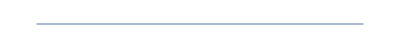

```mathematica
Region[tita]
```

```mathematica
(*Diagrama de bifurcaciones*)
nmax = 100000;
ntransitorio = 0;
tol = 0.001;

(*

*)

rmin = 1;
rmax =4;
pixeles = 1000;
definicion = (rmax - rmin)/pixeles;(*distancia entre r's sucesivos*)
xmin = 0.; (*sólo se usa en el gráfico*)
xmax = 1.; (*sólo se usa en el gráfico*)

(*Creo una lista de los rs sobre los que calculo los atractores*)
rbif = Range[rmin,rmax,definicion];
(*Busco iterativamente los atractores para cada r*)
(*⟦⟧*)
atractoresaux = {};
raux = {};

Do[r = rbif⟦k⟧;
If[Mod[k,10]== 0,Print["Progreso = ", N[100*k/Length[rbif],3], " %"]];
(*Print[Atractores[f,r,tol,nmax,ntransitorio]];*)
f[x_]:=r x (1-x);
atractoresaux = Join[atractoresaux,Atractores[f,r,tol,nmax,ntransitorio]];
raux = Join[raux,ConstantArray[rbif⟦k⟧,Length[atractoresaux] - Length[raux]]];
,{k,1,Length[rbif]}];

(*Print[atractoresaux];*)
```

Progreso = 0.999 %

Progreso = 2. %

Progreso = 3. %

Progreso = 4. %

Progreso = 5. %

Progreso = 5.99 %

Progreso = 6.99 %

Progreso = 7.99 %

Progreso = 8.99 %

Progreso = 9.99 %

Progreso = 11. %

Progreso = 12. %

Progreso = 13. %

Progreso = 14. %

Progreso = 15. %

Progreso = 16. %

Progreso = 17. %

Progreso = 18. %

Progreso = 19. %

Progreso = 20. %

Progreso = 21. %

Progreso = 22. %

Progreso = 23. %

Progreso = 24. %

Progreso = 25. %

Progreso = 26. %

Progreso = 27. %

Progreso = 28. %

Progreso = 29. %

Progreso = 30. %

Progreso = 31. %

Progreso = 32. %

Progreso = 33. %

Progreso = 34. %

Progreso = 35. %

Progreso = 36. %

Progreso = 37. %

Progreso = 38. %

Progreso = 39. %

Progreso = 40. %

Progreso = 41. %

Progreso = 42. %

Progreso = 43. %

Progreso = 44. %

Progreso = 45. %

Progreso = 46. %

Progreso = 47. %

Progreso = 48. %

Progreso = 49. %

Progreso = 50. %

Progreso = 50.9 %

Progreso = 51.9 %

Progreso = 52.9 %

Progreso = 53.9 %

Progreso = 54.9 %

Progreso = 55.9 %

Progreso = 56.9 %

Progreso = 57.9 %

Progreso = 58.9 %

Progreso = 59.9 %

Progreso = 60.9 %

Progreso = 61.9 %

Progreso = 62.9 %

Progreso = 63.9 %

Progreso = 64.9 %

Progreso = 65.9 %

Progreso = 66.9 %

Progreso = 67.9 %

Progreso = 68.9 %

Progreso = 69.9 %

Progreso = 70.9 %

Progreso = 71.9 %

Progreso = 72.9 %

Progreso = 73.9 %

Progreso = 74.9 %

Progreso = 75.9 %

Progreso = 76.9 %

Progreso = 77.9 %

Progreso = 78.9 %

Progreso = 79.9 %

Progreso = 80.9 %

Progreso = 81.9 %

Progreso = 82.9 %

Progreso = 83.9 %

Progreso = 84.9 %

Progreso = 85.9 %

Progreso = 86.9 %

Progreso = 87.9 %

Progreso = 88.9 %

Progreso = 89.9 %

Progreso = 90.9 %

Progreso = 91.9 %

Progreso = 92.9 %

Progreso = 93.9 %

Progreso = 94.9 %

Progreso = 95.9 %

Progreso = 96.9 %

Progreso = 97.9 %

Progreso = 98.9 %

Progreso = 99.9 %

```mathematica
(*Grafico*)
ListPlot[Transpose[{raux,atractoresaux}], PlotRange->{{rmin,rmax},{xmin,xmax}}, PlotMarkers->{Automatic,1}, Frame->True, AxesLabel->{r, x}]
```

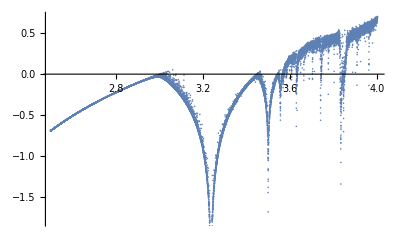

```mathematica
(*Exponente de Lyapunov*)


lambdar[r_,f_,fprima_,nmax_]:=Module[{ntransitorio, x0,lista,lambda},
(*Dado r y fprima, calcula lambda*)
ntransitorio = IntegerPart[nmax/10];
x0 = RandomReal[{0,1}];
lista = NestList[f,x0,nmax]⟦ntransitorio+1;;⟧;
lambda = 0;
Do[
lambda = lambda + Log[Abs[fprima[lista⟦i⟧]]]
,{i,1,Length[lista]}];
lambda = lambda/Length[lista]
]
```

```mathematica
nmax = 100;

rmin = 2.5;
rmax = 4;
definicion = 0.0001;
rlist = Range[rmin,rmax,definicion];

lambda = ConstantArray[0,Length[rlist]];
Do[
r = rlist⟦k⟧;
f[x_]:=r x (1-x);
fprima[x_] :=r (1-2 x); 
lambda⟦k⟧ =lambdar[r,f,fprima,nmax]
,{k,1,Length[rlist]}]
```

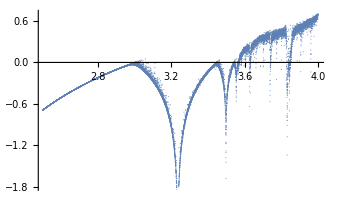

{0.8745,0.5005,0.8265,0.3825}

```mathematica
ListPlot[Transpose[{rlist,lambda}], Joined->False,PlotMarkers->{Automatic,1}]
```

```mathematica
(*Diagrama cobweb*)
```

```mathematica
cantx0 = 100;
x0s = RandomReal[{0,1},cantx0];
x0 = x0s⟦1⟧
```

0.707774

```mathematica
list=RandomReal[{0,999},100000];
Length[list]
pos=Ordering[list,-1];
Print[pos]
max=Extract[list,pos]
Length[list]
```

100000

{72852}

998.993

100000

```mathematica
x = {1,2,3,4}
```

{1,2,3,4}

{2,3,4}

Show::gcomb: Could not combine the graphics objects in ….